```mathematica
sig1=Table[Cos[2 π *0.03* k] +0.2*Cos[2 π *0.045* k] +0  (Random[]-0.5),{k,1,2048}];
sig2=Table[0.8*(Cos[2 π *0.03* k+2π*0.015] +0.22  Cos[2 π *0.045* k+2π*0.025 ])+0  (Random[]-0.5),{k,1,2048}];
sig3=Table[0.95*(Cos[2 π *0.03* k+2π*0.03] +0.2  Cos[2 π *0.045* k+2π*0.05])+0  (Random[]-0.5),{k,1,2048}];
sig4=Table[0.85*(Cos[2 π *0.03* k+2π*0.045] +0.15  Cos[2 π *0.045* k+2π*0.075])+0  (Random[]-0.5),{k,1,2048}];
```

```mathematica
SigL = List[sig1,sig2,sig3,sig4];
MatrixQ[SigL]
SigLT =Transpose[SigL];
MatrixForm[SigLT];
SigM = 1/2048 SigLT.SigL;
```

True

```mathematica
{u,w,v}=SVD=Chop[SingularValueDecomposition[SigM]];
MatrixForm[w]
```

(1)
 |  |  |  |

```mathematica
SVDFunc[x_,a_?NumberQ]:=ListPlot[Transpose[SingularValueDecomposition[x][[1;3]]][[a]],Joined->True, PlotRange->All]
```

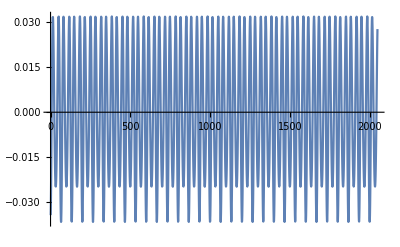

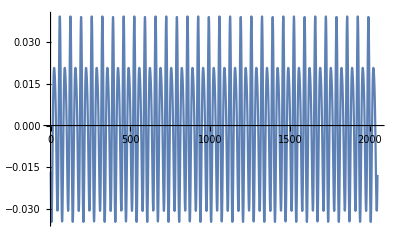

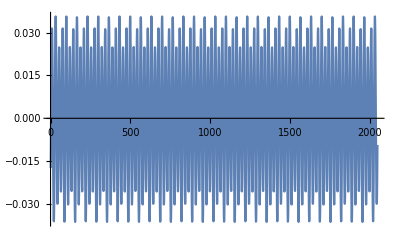

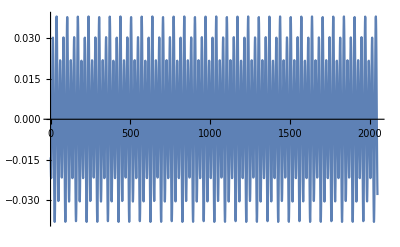

```mathematica
SVDFunc[SigM,1]
SVDFunc[SigM,2]
SVDFunc[SigM,3]
SVDFunc[SigM,4]
```

```mathematica
SVDVector[x_,a_?NumberQ]:=Transpose[SingularValueDecomposition[x][[1;3]]][[a]];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;NumPlace[x]+4]],AbsFourier[x][[1;;NumPlace[x]+4]]}],PlotRange->All]
```

```mathematica
SVDVector1 = SVDVector[SigM,1];
```

```mathematica
Freq[SVDVector1]
```

0.0297852

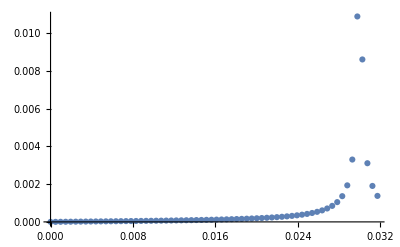

```mathematica
TruePlot[SVDVector1]
```

0.0297852

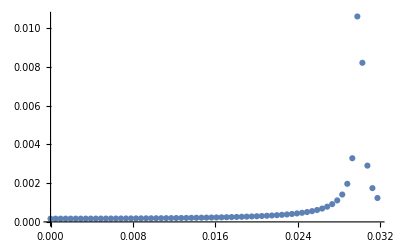

```mathematica
SVDVector2 = SVDVector[SigM,2];
Freq[SVDVector2]
TruePlot[SVDVector2]
```

0.0449219

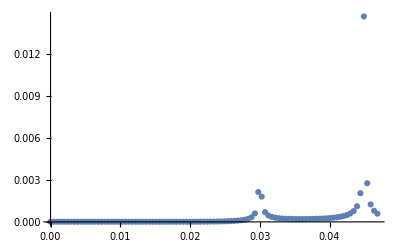

```mathematica
SVDVector3 = SVDVector[SigM,3];
Freq[SVDVector3]
TruePlot[SVDVector3]
```

0.0449219

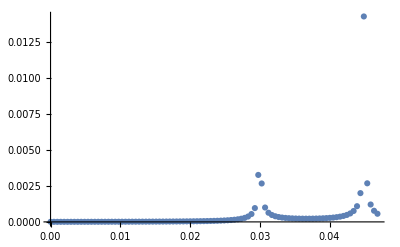

```mathematica
SVDVector4 = SVDVector[SigM,4];
Freq[SVDVector4]
TruePlot[SVDVector4]
```